### Compute half-mass

```mathematica
mhalf=FullSimplify[Assuming[{τ,X} ∈Reals && τ >1&&X>0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2)),{x,0,X}]]]
```

1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2])

### Compute total mass

```mathematica
mtot = FullSimplify[Assuming[{τ,X} ∈Reals && τ >1&&X>0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2)),{x,0,Infinity}]]]
```

(τ^2 (-1+(π-τ) τ+(-1+τ^2) Log[τ]))/((1+τ^2)^2)

### Plot the 2 cases for an examples

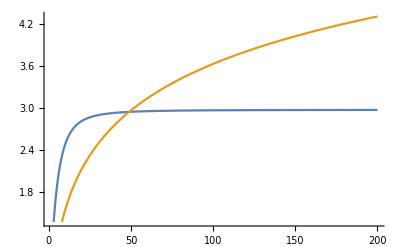

```mathematica
Plot[{2*mhalf/.X->10,mtot},{τ,1,200}]
```

### Ok they intersect, find solution numerically

```mathematica
tauSol[X_]:=FindRoot[(1/((1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2])) ==(τ^2 (-1+(π-τ) τ+(-1+τ^2) Log[τ]))/((1+τ^2)^2),{τ,X^1.7}]
```

### Make a table of solutions

```mathematica
τTab = Table[{X,tauSol[X][[1,2]]},{X,1,40,0.1}];
```

### Plot it

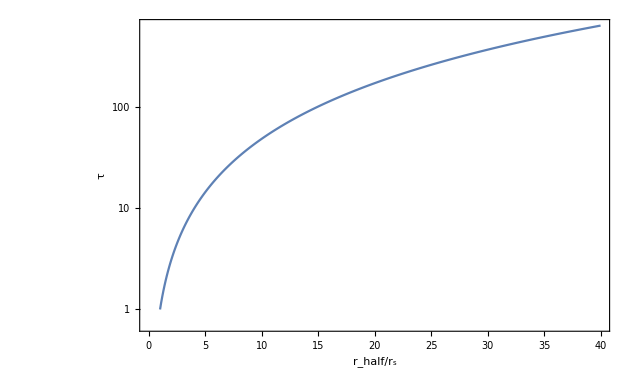

```mathematica
ListLogPlot[τTab,Joined-> True,Frame->True,FrameLabel-> {Subscript[r, half]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25]]
```

### Save to file

```mathematica
Export["tau_vs_xhalf.dat",τTab,"Data"]
```

tau_vs_xhalf.dat